```mathematica
Quit
```

```mathematica
<<"~/ownCloud/Shared/TenGSHui.m"
```

Loading TenGSHui...

Done. Please execute DisplayPalette if you need the palette.

```mathematica
ReloadPalette
```

89852613-ca83-4dbb-b9a0-436f16da6b51TenGSHui

```mathematica
ℓmax=100;
```

```mathematica
Rank[𝕦]^=1;
MaxDegree[𝕦]^=ℓmax;
𝕦[-1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((P[ℓ,𝓂][r])/r+P[ℓ,𝓂]'[r]-ⅈ T[ℓ,𝓂][r])
𝕦[0][ℓ_,𝓂_][r_]:=ℓ(ℓ+1)(P[ℓ,𝓂][r])/r
𝕦[1][ℓ_,𝓂_][r_]:=√((ℓ(ℓ+1))/2)((P[ℓ,𝓂][r])/r+P[ℓ,𝓂]'[r]+ⅈ T[ℓ,𝓂][r])
```

```mathematica
Rank[p]^=0;
MaxDegree[p]^=ℓmax;
p[][ℓ_,𝓂_][r_]:=𝓅[ℓ,𝓂][r]
```

```mathematica
Rank[N2]^=0;
MaxDegree[N2]^=0;
N2[][ℓ_,𝓂_][r_]:=r
```

```mathematica
Ω≐𝟙[𝕫]
```

```mathematica
Rank[ϑ]^=0;
MaxDegree[ϑ]^=ℓmax;
ϑ[][ℓ_,𝓂_][r_]:=θ[ℓ,𝓂][r]
```

```mathematica
eq≐(λ⋆𝕦⊕2⋆(Ω𝕦)⊕∇p⊕(-1⋆N2)⊗ϑ⊗𝕣)
```

```mathematica
theq≐λ⋆ϑ⊕(𝕦·𝕣)
```

```mathematica
𝓂=1;
ℒ=Join[Table[(eq)[0][ℓ,𝓂][r],{ℓ,2,ℓmax,2}],Table[(eq)[0][ℓ,𝓂][r],{ℓ,1,ℓmax,2}],Table[(theq)[][ℓ,𝓂][r],{ℓ,2,ℓmax,2}]]//Simplify;
```

```mathematica
ℬ=Table[P[ℓ,𝓂][1],{ℓ,2,ℓmax,2}]
```

{P[2,1][1],P[4,1][1],P[6,1][1],P[8,1][1],P[10,1][1],P[12,1][1],P[14,1][1],P[16,1][1],P[18,1][1],P[20,1][1],P[22,1][1],P[24,1][1],P[26,1][1],P[28,1][1],P[30,1][1],P[32,1][1],P[34,1][1],P[36,1][1],P[38,1][1],P[40,1][1],P[42,1][1],P[44,1][1],P[46,1][1],P[48,1][1],P[50,1][1],P[52,1][1],P[54,1][1],P[56,1][1],P[58,1][1],P[60,1][1],P[62,1][1],P[64,1][1],P[66,1][1],P[68,1][1],P[70,1][1],P[72,1][1],P[74,1][1],P[76,1][1],P[78,1][1],P[80,1][1],P[82,1][1],P[84,1][1],P[86,1][1],P[88,1][1],P[90,1][1],P[92,1][1],P[94,1][1],P[96,1][1],P[98,1][1],P[100,1][1]}

```mathematica
𝒱=Join[Table[P[ℓ,𝓂],{ℓ,2,ℓmax,2}],Table[T[ℓ,𝓂],{ℓ,1,ℓmax,2}],Table[θ[ℓ,𝓂],{ℓ,2,ℓmax,2}]]
```

{P[2,1],P[4,1],P[6,1],P[8,1],P[10,1],P[12,1],P[14,1],P[16,1],P[18,1],P[20,1],P[22,1],P[24,1],P[26,1],P[28,1],P[30,1],P[32,1],P[34,1],P[36,1],P[38,1],P[40,1],P[42,1],P[44,1],P[46,1],P[48,1],P[50,1],P[52,1],P[54,1],P[56,1],P[58,1],P[60,1],P[62,1],P[64,1],P[66,1],P[68,1],P[70,1],P[72,1],P[74,1],P[76,1],P[78,1],P[80,1],P[82,1],P[84,1],P[86,1],P[88,1],P[90,1],P[92,1],P[94,1],P[96,1],P[98,1],P[100,1],T[1,1],T[3,1],T[5,1],T[7,1],T[9,1],T[11,1],T[13,1],T[15,1],T[17,1],T[19,1],T[21,1],T[23,1],T[25,1],T[27,1],T[29,1],T[31,1],T[33,1],T[35,1],T[37,1],T[39,1],T[41,1],T[43,1],T[45,1],T[47,1],T[49,1],T[51,1],T[53,1],T[55,1],T[57,1],T[59,1],T[61,1],T[63,1],T[65,1],T[67,1],T[69,1],T[71,1],T[73,1],T[75,1],T[77,1],T[79,1],T[81,1],T[83,1],T[85,1],T[87,1],T[89,1],T[91,1],T[93,1],T[95,1],T[97,1],T[99,1],θ[2,1],θ[4,1],θ[6,1],θ[8,1],θ[10,1],θ[12,1],θ[14,1],θ[16,1],θ[18,1],θ[20,1],θ[22,1],θ[24,1],θ[26,1],θ[28,1],θ[30,1],θ[32,1],θ[34,1],θ[36,1],θ[38,1],θ[40,1],θ[42,1],θ[44,1],θ[46,1],θ[48,1],θ[50,1],θ[52,1],θ[54,1],θ[56,1],θ[58,1],θ[60,1],θ[62,1],θ[64,1],θ[66,1],θ[68,1],θ[70,1],θ[72,1],θ[74,1],θ[76,1],θ[78,1],θ[80,1],θ[82,1],θ[84,1],θ[86,1],θ[88,1],θ[90,1],θ[92,1],θ[94,1],θ[96,1],θ[98,1],θ[100,1]}

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","./spectral.m"];
Needs["sprouts`","./debug/sprouts.m"];
```

```mathematica
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,0,1},100,eigenvalue->λ]
```

partition of the spatial domain :  {{0,1}}

regularity conditions will be enforced at r=0 based on indices of spherical harmonics

eigenvalue problem of type :   (A0+A1 λ)x==0

Size of output matrices :  7500x7500

{SparseArray[<60619>, {7500, 7500}],SparseArray[…]}

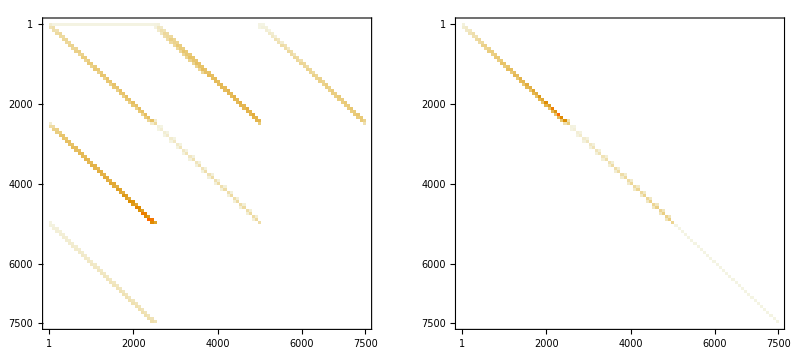

```mathematica
GraphicsRow[MatrixPlot/@Abs[A]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["./slepc/A0.mtx",A[[1]]/Norm[A[[2]],"Frobenius"]]
Export["./slepc/A1.mtx",A[[2]]/Norm[A[[2]],"Frobenius"]]
```

./slepc/A0.mtx

./slepc/A1.mtx